# Free Body Diagram

A free body diagram is a diagram that represents the forces applied on a certain object. Each force applied is represented by an arrow towards the force’s direction and labeled by it’s magnitude. The position of the arrow head will be equal to the x and y component of the forces as a coordinate. Below is an example of forces in vector form and the free body diagram is displayed underneath.

```mathematica
forces = {{4,0},{-4,3}}
```

{{4,0},{-4,3}}

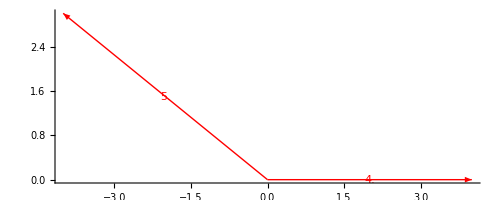

```mathematica
Graphics[{Thick,Arrowheads[Large],Red, Arrow[{{0,0},#}] & /@ forces, (Inset[Framed[Style[Round[Sqrt[#[[1]]^2 + #[[2]]^2],0.01],Black, 14], Background->White], {#[[1]]/2, #[[2]]/2}]) & /@ forces}, Axes->True, Method->{"AxesInFront"->False}]
```

## Transitional Equilibrium

Transitional Equilibrium a state where the sum of all forces for x and y components are equal to zero. Objects in transitional equilibrium always moves at constant speed.

ΣF = 0

#### Solving for Transitional Equilibrium

```mathematica
VectorEq[f_] := {-Sum[f[[i]][[1]],{i,1,Length[f]}],-Sum[f[[i]][[2]],{i,1,Length[f]}]}
```

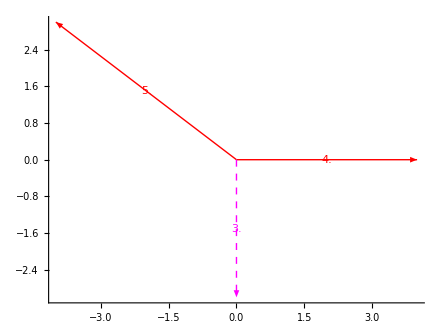

```mathematica
Graphics[{Thick,Arrowheads[Large],Red, Arrow[{{0,0},#}] & /@ forces,{Magenta,Dashed, Arrow[{{0,0}, VectorEq[forces]}], Inset[Framed[Style[Round[Sqrt[VectorEq[forces][[1]]^2 + VectorEq[forces][[2]]^2],0.01],Black,14],Background->White],{VectorEq[forces][[1]]/2, VectorEq[forces][[2]]/2}]}, (Inset[Framed[Style[Round[Sqrt[#[[1]]^2 + #[[2]]^2],0.01],Black, 14], Background->White], {#[[1]]/2, #[[2]]/2}]) & /@ forces}, Axes->True, Method->{"AxesInFront"->False}]
```